```mathematica
(* Uppgift 3)
```

```mathematica
(*Löser ekvationssystemet för att se vilka kordinater skärningspunkten är på.*)
```

```mathematica
Reduce[{x+2y+3z == 1, 2x+ 4y+7z == 2, 3x+7y+11z==8},{x,y,z}]
```

x==-9&&y==5&&z==0

```mathematica
(*Plottar det tre ekvationerna till ekvationssytemet och ser att skärningspunkten (lösningen) befinner sig på samma kordinater som (Reduce)operationen gav.*)
```

```mathematica
Show[ContourPlot3D[{x+2y+3z == 1, 2x+ 4y+7z == 2, 3x+7y+11z==8},{x,-10,10}, {y,-10,10},{z,-10,10},
AxesLabel->{"x","y","z"}],
Graphics3D[{Yellow, PointSize[0.1],Point[{-9,5,0}]}]]
```

-Graphics3D-

```mathematica
(*Uppgift 5*)
```

```mathematica
(*Löser ekvationssystemet för att se vilka kordinater skärningspunkten är på.*)
```

```mathematica
Reduce[{x-2y==3, 3x +5y ==17}, {x,y}]
```

x==49/11&&y==8/11

```mathematica
(*Plottar det två ekvationerna till ekvationssytemet och ser att skärningspunkten (lösningen) befinner sig på samma kordinater som (Reduce)operationen gav.*)
```

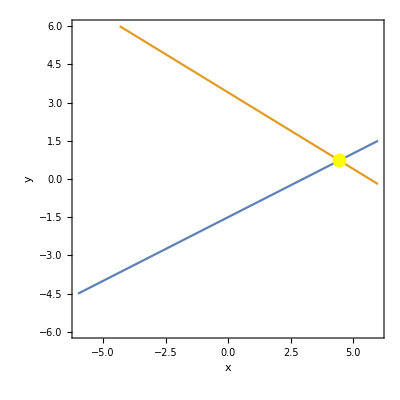

```mathematica
ContourPlot[{x-2y==3, 3x +5y ==17},{x,-6,6}, {y,-6,6}, AxesLabel->{"x","y"},
Epilog-> {Yellow, PointSize[0.025],Point[{49/11,8/11}]}]
```

```mathematica
(*Uppgift 6*)
```

```mathematica
(*Löser ekvationssystemet för att se vilka kordinater skärningspunkten är på. I detta fallet så saknar ekvationen lösning och (Reduce) operationen säger därmed "False".*)
```

```mathematica
Reduce[{3x+4y-z==8, 6x +8y -2z==3}, {x,y,z}]
```

False

```mathematica
(*Plottar det två ekvationerna till ekvationssytemet och ser att det inte finns någon skärningspunkten då plannen är parallella med varandra. man såg även detta då det finns 3st obekanta variabler men bara 2st ekvationssystem.*)
```

```mathematica
ContourPlot3D[{3x+4y-z==8, 6x +8y -2z==3},{x,-10,10}, {y,-10,10},{z,-10,10}, AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
(*Uppgift 7*)
```

```mathematica
(*Konstruerar matriserna a,b och c och tilldelar deras inehåll.*)
```

```mathematica
a = ({{3, 2, 4}, {7, 12, 0}, {2, 5, 2}})
```

{{3,2,4},{7,12,0},{2,5,2}}

```mathematica
c = ({{5, 22, 5}, {5, 9, 7}, {6, 8, 2}})
```

{{5,22,5},{5,9,7},{6,8,2}}

```mathematica
b = ({{5, 8, 7}, {6, 4, 9}, {10, 1, 0}})
```

{{5,8,7},{6,4,9},{10,1,0}}

```mathematica
(*Utför operationen a - b + c*)
```

```mathematica
MatrixForm[a - b + c]
```

```mathematica
({{3, 16, 2}, {6, 17, -2}, {-2, 12, 4}})
```

{{3,16,2},{6,17,-2},{-2,12,4}}

```mathematica
(*Utför operationen abc*)
```

```mathematica
MatrixForm[a  . b . c]
```

```mathematica
({{749, 2110, 665}, {1997, 4546, 1577}, {844, 2134, 684}})
```

{{749,2110,665},{1997,4546,1577},{844,2134,684}}

```mathematica
(*Utför operationen CBA*)
```

```mathematica
MatrixForm[c . b . a]
```

```mathematica
({{2018, 3175, 1294}, {1260, 1874, 828}, {1096, 1750, 620}})
```

{{2018,3175,1294},{1260,1874,828},{1096,1750,620}}

```mathematica
(*Uppgift 8*)
```

```mathematica
(*Utför RowReduce på matrisen för att hitta matrisens rref.*)
```

```mathematica
RowReduce[{{2, 4, 8}, {4, 5, 1}, {7, 9, 3}}]
```

{{1,0,-6},{0,1,5},{0,0,0}}

```mathematica
(*Utför Matrixform för den rref matrisen för att visualisera resultatet i matrisform.*)
```

```mathematica
MatrixForm[%]
```

(1 | 0 | -6
0 | 1 | 5
0 | 0 | 0)

```mathematica
(*Matrisen har redudans då det inte finns någon UNIK lösning som tillfredställer alla ekvationer. "0 0 0" på den understa raden i matrisen.*)
```

```mathematica
(*Uppgift 9*)
```

```mathematica
(*Använder Eigenvalues operationen med värderna i den givna matrisen för att få fram egenvärderna för matrisen.*)
```

```mathematica
Eigenvalues[{{9, -4, -2, -4},{-56, 32, -28, 44},{-14, -14, 6, -14}, {42, -33, 21, -45}}]
```

{13,13,-12,-12}

```mathematica
(*Svar: 13, 13, -12, -12*)
```

```mathematica
(*Uppgift 2*)
```

```mathematica
(*För att hitta vinkeln mellan vektorerna använder jag VectorAngle operationen och får ut att vinkeln är ArcCos[√(6/7)].*)
```

```mathematica
VectorAngle[{2,-2,-2},{3,-2,-1}]
```

ArcCos[√(6/7)]

```mathematica
(*Detta steg är inte obligatoriskt men ville visualisera det två vektorerna i det tredimensionella rummet.*)
```

```mathematica
Graphics3D[{Thick,Line[{{0,0,0},{2,-2,-2}}],Line[{{0,0,0},{3,-2,-1}}]}]
```

-Graphics3D-

```mathematica
(*Uppgift 2.6 (13) i Lay*)
```

```mathematica
(* Leontief-modellen:Lös uppgift 13 i kursboken av Lay (ed.6),kapitel 2.6,sid 170.*)
(*Matrisen I-C är*)
```

```mathematica
DiagonalMatrix[{1,1,1,1,1,1,1}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
i=({{1, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 1}});
c=({{0.1588, 0.0064, 0.0025, 0.0304, 0.0014, 0.0083, 0.1594}, {0.0057, 0.2645, 0.0436, 0.0099, 0.0083, 0.0201, 0.3413}, {0.0264, 0.1506, 0.3557, 0.0139, 0.0142, 0.0070, 0.0236}, {0.3299, 0.0565, 0.0495, 0.3636, 0.0204, 0.0483, 0.0649}, {0.0089, 0.0081, 0.0333, 0.0295, 0.3412, 0.0237, 0.0020}, {0.1190, 0.0901, 0.0996, 0.1260, 0.1722, 0.2386, 0.3369}, {0.0063, 0.0126, 0.0196, 0.0098, 0.0064, 0.0132, 0.0012}});
'
MatrixForm[i-c]
```

(0.8412 | -0.0064 | -0.0025 | -0.0304 | -0.0014 | -0.0083 | -0.1594
-0.0057 | 0.7355 | -0.0436 | -0.0099 | -0.0083 | -0.0201 | -0.3413
-0.0264 | -0.1506 | 0.6443 | -0.0139 | -0.0142 | -0.007 | -0.0236
-0.3299 | -0.0565 | -0.0495 | 0.6364 | -0.0204 | -0.0483 | -0.0649
-0.0089 | -0.0081 | -0.0333 | -0.0295 | 0.6588 | -0.0237 | -0.002
-0.119 | -0.0901 | -0.0996 | -0.126 | -0.1722 | 0.7614 | -0.3369
-0.0063 | -0.0126 | -0.0196 | -0.0098 | -0.0064 | -0.0132 | 0.9988)

```mathematica
(*Så den förändrade matrisen [i-c d] kan radreduceras och det blir följande*)
```

```mathematica
m =({{0.8412, -0.0064, -0.0025, -0.0304, -0.0014, -0.0083, -0.1594, 74000}, {-0.0057, 0.7355, -0.0436, -0.0099, -0.0083, -0.0201, -0.3413, 56000}, {-0.0264, -0.1506, 0.6443, -0.0139, -0.0142, -0.007, -0.0236, 10500}, {-0.3299, -0.0565, -0.0495, 0.6364000000000001, -0.0204, -0.0483, -0.0649, 25000}, {-0.0089, -0.0081, -0.0333, -0.0295, 0.6588, -0.0237, -0.002, 17500}, {-0.119, -0.0901, -0.0996, -0.126, -0.1722, 0.7614, -0.3369, 196000}, {-0.0063, -0.0126, -0.0196, -0.0098, -0.0064, -0.0132, 0.9988, 5000}})
MatrixForm[RowReduce[m]]
```

{{0.8412,-0.0064,-0.0025,-0.0304,-0.0014,-0.0083,-0.1594,74000},{-0.0057,0.7355,-0.0436,-0.0099,-0.0083,-0.0201,-0.3413,56000},{-0.0264,-0.1506,0.6443,-0.0139,-0.0142,-0.007,-0.0236,10500},{-0.3299,-0.0565,-0.0495,0.6364,-0.0204,-0.0483,-0.0649,25000},{-0.0089,-0.0081,-0.0333,-0.0295,0.6588,-0.0237,-0.002,17500},{-0.119,-0.0901,-0.0996,-0.126,-0.1722,0.7614,-0.3369,196000},{-0.0063,-0.0126,-0.0196,-0.0098,-0.0064,-0.0132,0.9988,5000}}

(1 | 0. | 0. | 0. | 0. | 0. | 0. | 99589.1
0 | 1 | 0. | 0. | 0. | 0. | 0. | 97733.7
0 | 0 | 1 | 0. | 0. | 0. | 0. | 51249.9
0 | 0 | 0 | 1 | 0. | 0. | 0. | 131645.
0 | 0 | 0 | 0 | 1 | 0. | 0. | 49522.7
0 | 0 | 0 | 0 | 0 | 1 | 0. | 330368.
0 | 0 | 0 | 0 | 0 | 0 | 1 | 13847.9)

```mathematica
(*Svar: x ≈ (100000, 98000, 51000, 132000, 49000, 330000, 14000 vilket är produktions nivåerna som tillfredställer efterfrågan d (Millions of dollars)(*)
```

```mathematica
(*Uppgift 16: Avgör om följande uppsättning polynom utgör en bas för vektorrummet P3. {5 - 3t + 4t^2 + 2t^3, 9 + t + 8t^2 - 6t^3, 6 - 2t + 5t^2, t^2}*)
```

```mathematica
(*Steg 1: namge varje polynom till vektor: s = {5 - 3t + 4t^2 + 2t^3, 9 + t + 8t^2 - 6t^3, 6 - 2t + 5t^2, t^2} där polynom nr 1 är V1, polynom nr2 V2 osv.*)
```

```mathematica
(*Steg 2: Följer deffinitionen av linjär kombination av vektorerna: C1V1 + C2V2 + C3V3 + C4V4 = 0*)
```

```mathematica
(*Steg 3: substitura in vektorerna: C1(5 - 3t + 4t^2 + 2t^3) + C2(9 + t + 8t^2 - 6t^3) + C3(6 - 2t + 5t^2) + C4(t^2) = 0 *)
```

```mathematica
(*Steg 4: Faktorisera ut t: t^3(2C1 - 6C2) + t^2(4C1 + 8C2 + 5C3 + C4) + t^1(-3C1 + C2 - 2C3) + t^0(5C1 + 9C2 + 6C3) = 0 *)
```

```mathematica
(*Steg 5: konstruera ekvationsystem: {(2C1 - 6C2 = 0), (4C1 + 8C2 + 5C3 + C4 = 0), (-3C1 + C2 - 2C3 = 0), (5C1 + 9C2 + 6C3 = 0)}*)
```

```mathematica
(*Steg 6: konstruera matris:*)
```

```mathematica
w = ({{2, -6, 0, 0}, {4, 8, 5, 1}, {-3, 1, -2, 0}, {5, 9, 6, 0}})
MatrixForm[RowReduce[w]]
```

{{2,-6,0,0},{4,8,5,1},{-3,1,-2,0},{5,9,6,0}}

(1 | 0 | 3/4 | 0
0 | 1 | 1/4 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

```mathematica
(*2st pivo columner (V1 & V2) (5 - 3t + 4t^2 + 2t^3, 9 + t + 8t^2 - 6t^3) Dimw = 2. Svar: Följande uppsättning utgör en bas i vaktorrummet P3.*)
```

```mathematica
(*Uppgift 11*)
```

```mathematica
(*Sätter upp transform matrisen tx och startvektorn x*)
```

```mathematica
MatrixForm[tx={{1, 1}, {-1, 1}}];
x={0,1};

(*r antal element, c som array fyllda med våra transformationer, c[0] är vårat första elemnt. Sedan använder jag en for-loop för att iterara genom den första listan och utför transformation på varje steg i arrayen*)

r=4;
c=Table[0, {r}];
c[[0]]=x;
For[p=1,p≤r,p++,v[[p]]= tx.v[[p-1]]];

(*Nu kan vi få elementen att ligga i våran array c och vi kan nu representera resultatet i en graf. Jag väljer Grphics och arrow för att representera det olika vektorerna*)

v
```

{0,1}[{1,1},{2,0},{2,-2},{0,-4}]

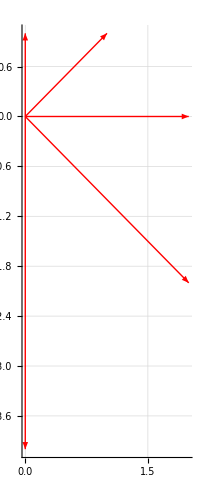

```mathematica
Show[Graphics[{Red,Arrow[{{0,0},{0,1}}],Red,Arrow[{{0,0},{1,1}}],Red,Arrow[{{0,0},{2,0}}],Red,Arrow[{{0,0},{2,-2}}],Red,Arrow[{{0,0},{0,-4}}]},Axes->True,GridLines->Automatic]]
```

```mathematica
(*Svar: Transformationen skalar upp i storlek och roterar medurs 45 grader*)
```